Зад.1 Докажете неравенството между средно аритметично и средно геометрично
 (x + y)/2 ≥ √(x y),
където x и y са неотрицателни реални числа.

```mathematica
Simplify[(x+y)/2≥ √(x y),{x≥ 0,y≥0}]
```

True

```mathematica
Зад.2 Направете предположение за корените на полинома p(x) = 2 x^5+5 x^4-8 x^3-14 x^2+6x + 9, като начертаете графиката му в подходящ интервал. Проверете предположенията си, като разложите полинома на неразложими множители.
```

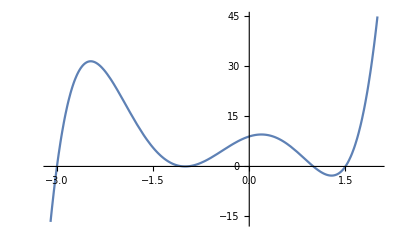

```mathematica
Plot[2 x^5+5 x^4-8 x^3-14 x^2+6x+9,{x,-3.1,2}]
```

```mathematica
Factor[2 x^5+5 x^4-8 x^3-14 x^2+6x+9]
```

(-1+x) (1+x)^2 (3+x) (-3+2 x)

Зад.3 Да се напише функция, която приема като параметър комплексно число и връща абсолютната му стойност  | z | = √([Re(z)]^2+[Im(z)]^2).
	(а) Функцията да се тества с числата z_1 = 2ⅈ + 5 и  z_2 = 4ⅈ + 4, като резултатът се сравни със стойността, която връща съответната вградена функция;
	(б) Да се визуализират z_1 и  z_2  като точки в комплексната равнина, заедно с отсечките, изобразяващи разстоянието им от центъра на координатната система (отсечките да се начертаят с прекъсната линия) и да се поставят подходящи означения на двете оси.
*Допълнителна задача: Да се напише функция, която за произволно комплексно число, визуализира графиката, описана в подточка (б).

```mathematica
findModulus[z_]:=√((Re[z])^2+(Im[z])^2)
```

```mathematica
findModulus[2ⅈ+5]==Abs[2ⅈ+5]
findModulus[4ⅈ+4]== Abs[4ⅈ+4]
```

True

True

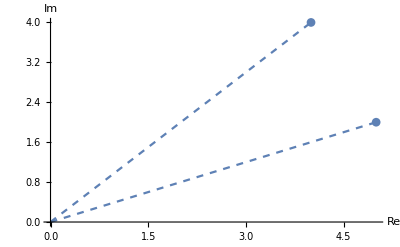

```mathematica
Show[ListPlot[{{5,2},{4,4}},PlotMarkers->Automatic,AxesLabel->{Re,Im}],
Plot[x,{x,4,0},PlotStyle->Dashed],
Plot[(2/5x),{x,0,5},PlotStyle->Dashed],
PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
complexNumberVisualise[z_]:=(
Show[ListPlot[{{Re[z],Im[z]}},PlotMarkers->Automatic,AxesLabel->{Re,Im}],
Plot[Im[z]/Re[z]x,{x,0,Re[z]},PlotStyle->Dashed],
PlotRange->All,AxesOrigin->{0,0}]
)
```

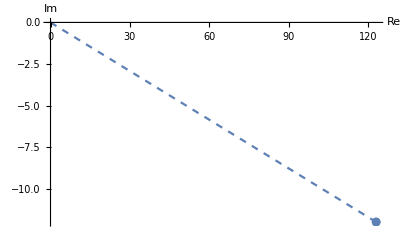

```mathematica
complexNumberVisualise[-12ⅈ+123]
```

Зад.4 В една държава, дължимият данък върху доходите на дадено лице се изчислява както следва.
 Доходи на стойност до $10 000 не се облагат с данъци. Доходи между $10 000 и  $20 000 се облагат с 10% от получената сума, а за доходи над $20 000, данъкоплатците дължат на държавата 15% от получената сума.
(а) Да се дефинира данъчната ставка (дължимия данък в проценти) като функция на дохода и да се начертае графиката на тази функция;
(б) Да се начертае графика на дължимата сума по данъка като функция на дохода.
Да се свържат отделните части на функцията с прекъсната линия и да се добавят подходящи заглавия на фигурите и осите.

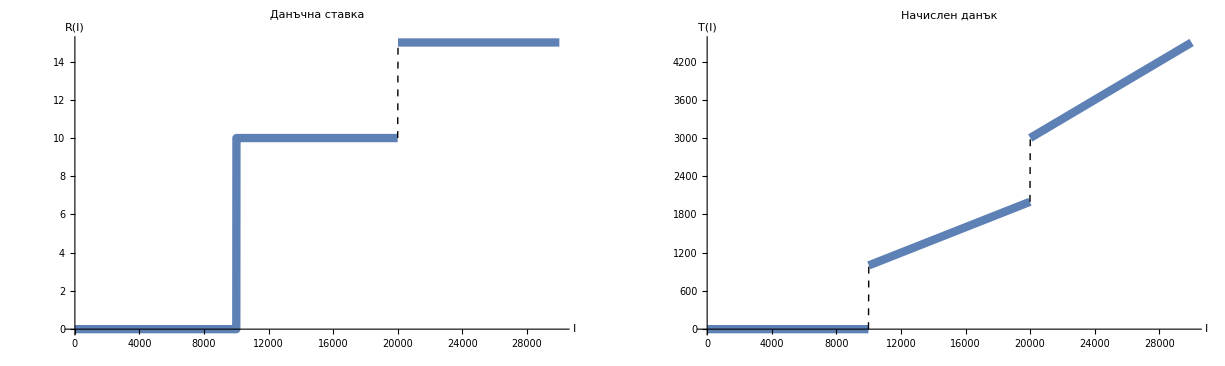

```mathematica
R[x_]:=Piecewise[{{0, x≤10000}, {10, 10000<x≤20000}, {15, True}}]
GraphicsRow[{Plot[R[x],{x,0,30000},Exclusions->{10000,20000},ExclusionsStyle->Dashed,PlotStyle->Thickness[0.015],PlotLabel->"Данъчна ставка", AxesLabel->{"I","R(I)"}],
Plot[R[x]/100 x,{x,0,30000},Exclusions->{10000,20000},ExclusionsStyle->Dashed,PlotStyle->Thickness[0.015],PlotLabel->"Начислен данък", AxesLabel->{"I","T(I)"}]}]
```

Зад.5 Основният математически труд на италианския математик Джироламо Кардано е свързан с решаването на полиномиални уравнения от трета и четвърта степен. Опитите му да намери аналитично решение на уравненията от трета степен водят до откриването на имагинерните числа, но те стават популярни доста по-късно, след публикации на други математици. 

Формулата на Кардано

x = (-q/2+√(q^2/4+p^3/27))^(1/3)+(-q/2-√(q^2/4+p^3/27))^(1/3)

 дава един от корените на кубично уравнение от вида
 
 x^3+p x+ q= 0.           (1)
 
Проверете дали кубичния полином (2 - √3+ x) (-4 + x )(2 + √3+ x) е от вида (1). Ако да, пресметнете един от корените му по формулата на Кардано.

```mathematica
Expand[(2-√3+x) (-4+x)(2+√3+x)]
 (-q/2+√(q^2/4+p^3/27))^(1/3)+(-q/2-√(q^2/4+p^3/27))^(1/3)/.{p->-15,q->-4}
```

-4-15 x+x^3

4